```mathematica
Map[First,ConversionMatrix["C","F"]*24//Flatten//Abs//Tally//Sort]
```

{0,1,2,3,4,6,8,10,11,12,18,24}

```mathematica
(allGraphs5[lambdaKey,"colofournull"]//Expand)/.RepGraph["F"]
```

(-Graphics-1969213)/6-(-Graphics-1968615)/3+(-Graphics-1968413)/6+(-Graphics-664216)/6+(-Graphics-658816)/6-(-Graphics-656215)/3-(-Graphics-243015)/3+(-Graphics-221416)/6+(-Graphics-219016)/6+(-Graphics-97213)/6-(-Graphics-81015)/3+(-Graphics-73813)/6+(-Graphics-24413)/6+(-Graphics-8416)/6-(-Graphics-3615)/3+(-Graphics-264885)/3-(-Graphics-219545)/6+(-Graphics-204485)/3+(-Graphics-196965)/3-(-Graphics-87845)/6-(-Graphics-73745)/6-(-Graphics-66705)/6+(-Graphics-31605)/3-(-Graphics-24605)/6+(-Graphics-10625)/3+(-Graphics-295240)/6

```mathematica
(allGraphs5[lambdaKey,"colofournull"]//Expand)
```

p12345/6+p123x45/3-p124x35/6+p125x34/3+p12x345/3+p12x34x5/6-p12x35x4/3+p12x3x45/6-p134x25/6-p135x24/6-p13x245/6+p13x24x5/6+p13x25x4/6-p13x2x45/3+p145x23/3-p14x235/6-p14x23x5/3+p14x25x3/6+p14x2x35/6+p15x234/3+p15x23x4/6-p15x24x3/3+p15x2x34/6+p1x23x45/6+p1x24x35/6-p1x25x34/3

```mathematica
(allGraphs5[lambdaKey,"colofournull"]//Factor)/.RepChromial["F"]
```

1/6 (24 x-40 x^2+20 x^3-10 x^4+6 x^5+10 (-2 x^2+5 x^3-4 x^4+x^5)-10 (x^3-2 x^4+x^5))

```mathematica
Table[Coefficient[allGraphs5[k,"colofournull"],p12345],{k,Keys[allGraphs5]}]//Sort//Tally
```

{{-1/4,10},{-1/6,60},{-1/8,30},{-1/12,120},{-1/24,175},{0,671},{1/24,201},{1/12,175},{1/8,60},{1/6,147},{1/4,80},{7/24,10},{1/3,70},{5/12,30},{1/2,30},{7/12,15},{3/4,10},{1,1}}

```mathematica
Table[
Fold[LCM,Map[First,Abs[Select[Table[Coefficient[allGraphs5[k,"colofournull"],var],{k,Keys[allGraphs5]}],#≠0&]//Sort]//Tally]],
{var,Bases["F","Variables"]}]//DeleteDuplicates//Sort//MatrixForm
```

(1
10
30
105
2310)

```mathematica
Table[
Fold[LCM,Map[First,Abs[Select[Table[Coefficient[allGraphs5[k,"colofourrealnull"],var],{k,Keys[allGraphs5]}],#≠0&]//Sort]//Tally]],
{var,Bases["E","Variables"]}]//DeleteDuplicates//Sort//MatrixForm
```

(1
2
12
2520)

```mathematica
Table[
Fold[LCM,Map[First,Abs[Select[Table[Coefficient[allGraphs5[k,"colofour"],var],{k,Keys[allGraphs5]}],#≠0&]//Sort]//Tally]],
{var,Bases["C","Variables"]}]//DeleteDuplicates//Sort//MatrixForm
```

(1)

```mathematica
Table[
Fold[LCM,Map[First,Abs[Select[Table[Coefficient[allGraphs5[k,"colofourgenerator"],var],{k,Keys[allGraphs5]}],#≠0&]//Sort]//Tally]],
{var,Bases["G","Variables"]}]//DeleteDuplicates//Sort//MatrixForm
```

(1
2
60
27720)

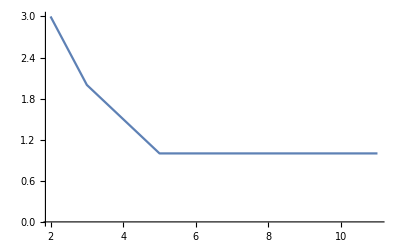

```mathematica
FactorInteger[27720]//ListLinePlot
```

```mathematica
LCM[1/12,1/6]
```

1/6